# Week 3:

## Sunday 24/3

Plotting Phase-Space

```mathematica
V=m g l(1-Cos[ϕ]);
T=(m l^2)/2(D[ϕ[t],t])^2;
H=T+V;
m=1;g=1;l=1;
f1=Table[H==k/.{ϕ[t]-> ϕ,ϕ'[t]-> p},{k,0,20,0.2}];
```

```mathematica
ContourPlot[Evaluate[f1],{ϕ,-π,π},{p,-π,π}]
```

Finding Time-Period - Series

```mathematica
k=Sin[ϕ1/2];
z=Sin[ϕ/2]/k/.ϕ1-> 0.2π;
```

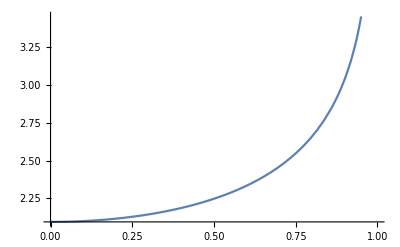

```mathematica
T1=4/ω0 Integrate[1/(√((1-z^2)(1-k^2 z^2))),{z,0,1}, Assumptions-> {k>0 && k<1}]/. ω0-> 3;
Plot[T1,{k,0,1}]
```

```mathematica
S1=Series[T1,{k,0,10}];
res1=Normal[S1];
```

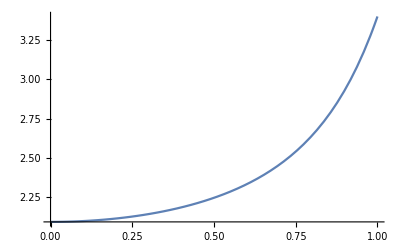

```mathematica
Plot[res1,{k,0,1}]
```

```mathematica
f1=Normal[Series[1/(√((1-z^2)(1-k^2 z^2))),{k,0,10}]];
T2=Expand[4/ω0 Integrate[f1,{z,0,1}, Assumptions-> {k>0 && k<1}]];
```

Expand = Expands T2 as a function different powers of k.

A bit about Mathematica

Mathematica “remembers” functions in tree forms - TreeForm[a]
The “head” of the tree is f - Head[a].
The function Part and [[]] are the same : Part[a,2,1]= a[[2,1]]
Which means - take the second part of a and choose section one of it.
MORE INFO IN THE LECTURES NOTES.

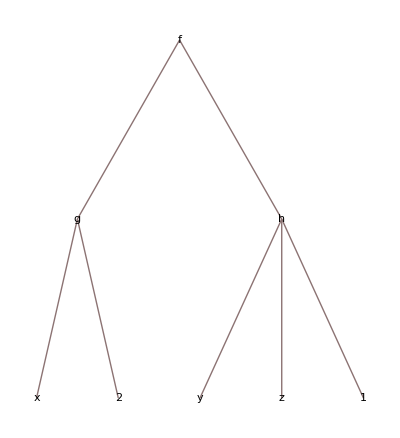

```mathematica
a=f[g[x,2],h[y,z,1]];
TreeForm[a]
Head[a]
```

## Tuesday 26/3

Iterative functions:

One can build an iterative function as “factorial” like  so:

```mathematica
fac[0]=1;
fac[n_]:=n fac[n-1];
fac[3]
```

Solving analytically the mathematical pendulum:

```mathematica
eq=DSolve[ϕ''[t]==-ω^2 Sin[ϕ[t]],ϕ[t],t];
eq1=eq[[1]]/. {C[1]-> 1 , C[2]-> 1, ω-> 1};
```

```mathematica
s1=Normal[N[Series[-2 JacobiAmplitude[1/2 √3 √((1+t)^2),4/3],{t,0,4}]]]//Chop
```

-1.48948-1.07817 t+0.498348 t^2+0.0145964 t^3-0.051649 t^4

Instead of  //Chop one can use the function - ComplexExpand[Re[s1]]
N[]  transform Analytic expressions like sin or the KacobiAmplitude into numbers - like the one I got in the end.

Solving numerically the mathematical pendulum:

Now I write ϕ as x, I will take the same initial conditions as for the analytical solution - x[0]=-1.48948 and x’[0]=-1.07817 and ω=1.

```mathematica
x=x0+Sum[a[i] t^i,{i,4}]+O[t]^5;
D[x,{t,2}]+ω^2 Sin[x]==0;
LogicalExpand[%];
sol=Solve[%]/.ω-> 1;
res1=x/.sol[[1]];
a[1]=-1.07817; x0=-1.48948;
N[res1]//Chop
```

-1.48948-1.07817 t+0.498348 t^2+0.014596 t^3-0.0516487 t^4+O[t]^5

Which is The same as we got when we solved the equation analytically.

# Week 4:

## Sunday 31/3

## Tuesday 2/4